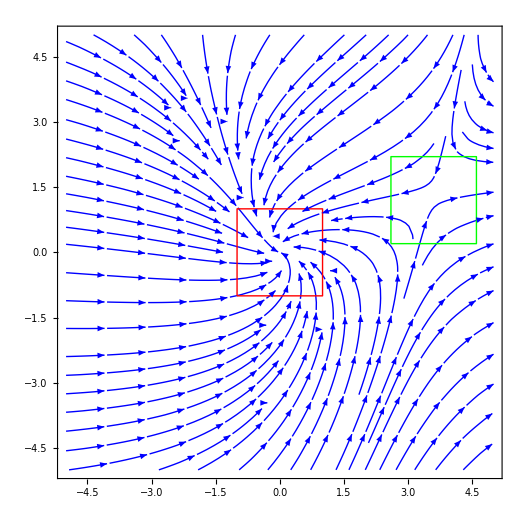

```mathematica
box[{x_,y_},{X_,Y_}]:=Line[{{x,y},{x,Y},{X,Y},{X,y},{x,y}}];

A=StreamPlot[{x^2/3-x-y/2,x/4-y+y/3},{x,-5,5},{y,-5,5},StreamStyle->Blue,StreamPoints-> 100, StreamScale->0.09];
B=Graphics[{Red, Thick,box[{-1,-1},{1,1}]}];
G=Graphics[{Green, Thick,box[{2.6,0.2},{4.6,2.2}]}];

Show[A,B,G]
```